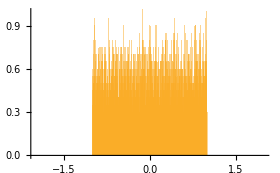

```mathematica
(* Simple central limit theorem example *)

dataL=RandomVariate[UniformDistribution[{-1.0,1.0}],10000];

Show[Histogram[{dataL},1000,"ProbabilityDensity",PlotRange->{{-2,2},{0.00,1.0}}]]
```

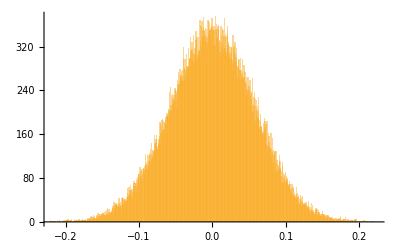

```mathematica
dataN={};
For[i=0,i<100000,i++; dataL=RandomVariate[UniformDistribution[{-1.0,1.0}],100]; AppendTo[dataN,Mean[dataL]]];
Show[Histogram[{dataN},1000]]
```

```mathematica
(* now test if data is normally distributed *)
DistributionFitTest[dataN]
HH=DistributionFitTest[dataN,Automatic,"HypothesisTestData"];
HH["TestDataTable",All]
```

0.901749

| Statistic | P-Value
Anderson-Darling | 0.218606 | 0.844228
Baringhaus-Henze | 0.301912 | 0.991177
Cramér-von Mises | 0.0266032 | 0.901749
Jarque-Bera ALM | 2.2906 | 0.318129
Kolmogorov-Smirnov | 0.00144478 | 0.912685
Kuiper | 0.00247391 | 0.951929
Mardia Combined | 2.2906 | 0.318129
Mardia Kurtosis | -1.2895 | 0.197224
Mardia Skewness | 0.637469 | 0.424629
Pearson χ^2 | 182.592 | 0.761319
Watson U^2 | 0.0231541 | 0.919031

```mathematica
(* what is the p-value? *)
(* DistributionFitTest performs a goodness of fit hypothesis test with null hypothesis that data was drawn from a population with distribution distBy default,a probability value or p-value is returned. A small value suggests that it is unlikely that the data came from dist. So: what is the probability to obtain the observed sampled if the assumed, underlying distribution is in fact true.*)
```

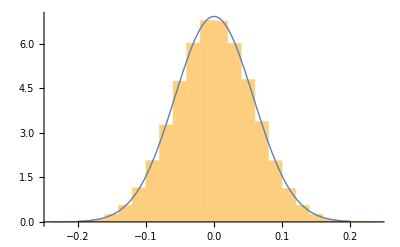

```mathematica
Show[Histogram[dataN,Automatic,"ProbabilityDensity"],Plot[PDF[HH["FittedDistribution"],x],{x,-0.2,0.2},PlotStyle->Thick]]
```